## Localization transition in the Aubry-André-Harper model

This notebook uses the QuLib library. 
More details can be found in http://www.fmt.if.usp.br/~gtlandi/qulib.html

```mathematica
SetDirectory[NotebookDirectory[]];
Get["http://www.fmt.if.usp.br/~gtlandi/download/qulib.m"]
SetOptions[ListPlot,Filling->Axis,PlotMarkers->Automatic,Joined->True,PlotRange->{{1,All},All}];

SetOptions[ArrayPlot,FrameTicks->Automatic,FrameLabel->{"eigenvec","site"},BaseStyle->{FontFamily->"Times",14},ImageSize->280];
```

### 1) Constructing a Hamiltonian

The function below constructs tight-binding Hamiltonians of size L, with arbitrary diagonal entries ϵ_n. 
The off-diagonals are chosen as g = 1 in all cases.

```mathematica
H[ϵvec_]:= DiagonalMatrix[ϵvec] + DiagonalMatrix[ConstantArray[-1.,Length@ϵvec-1],1]+DiagonalMatrix[ConstantArray[-1.,Length@ϵvec-1],-1]
```

For instance

```mathematica
ϵvec = {1,2,3,4,5};
H[ϵvec]//mf;
```

(1. | -1. | 0. | 0. | 0.
-1. | 2. | -1. | 0. | 0.
0. | -1. | 3. | -1. | 0.
0. | 0. | -1. | 4. | -1.
0. | 0. | 0. | -1. | 5.)

The function “// mf” is a trick for better visualizing the matrix.

### 2) Computing eigenvalues and eigenvectors

To compute the eigenthings, I recommend you use the function Eigsys from qulib (it correctly orders the energies in increasing order)

```mathematica
{vals,vecs}=Eigsys[H[ϵvec]]
```

{{0.253842,1.79227,3.,4.20773,5.74616},{{0.777047,0.5798,0.235374,0.0665753,0.0140272},{-0.542495,0.429801,0.631779,0.333219,0.10388},{-0.301511,0.603023,-0.301511,-0.603023,-0.301511},{-0.10388,0.333219,-0.631779,0.429801,0.542495},{0.0140272,-0.0665753,0.235374,-0.5798,0.777047}}}

The output is a list {values, vectors} containing all the eigenvalues and the corresponding eigenvalues.

```mathematica
vals
```

{0.253842,1.79227,3.,4.20773,5.74616}

The eigenvector associated with eigenvalue 1.79227 is

```mathematica
vecs[[2]]
```

{-0.542495,0.429801,0.631779,0.333219,0.10388}

### 3) Plotting probabilities

Recall that, given an eigenvector ψ⃗, the entries ψ_n are such that |ψ_n|^2 is the probability of finding the system at site n. We can thus plot this:

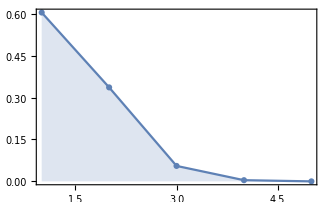

```mathematica
ListPlot[Abs[vecs⟦1⟧]^2]
```

Each eigenvector will have a different probability

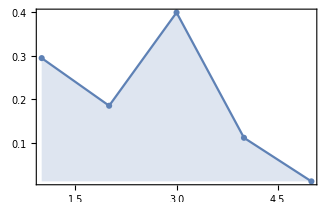

```mathematica
ListPlot[Abs[vecs⟦2⟧]^2]
```

The smallest energy (eigenvalue) is called the ground state. Higher eigenvalues are called the excited states.

You can also plot all of them together using ArrayPlot:

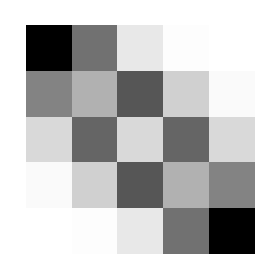

```mathematica
ArrayPlot[Abs[vecs]^2]
```

Sometimes the contrast is not very good if you plot Abs[vecs]^2. 
For better visualization you can plot, for instance Abs[vecs]^(1/2).

## The exercise

Construct the Aubry-André-Harper Hamiltonian for 100 sites, with λ = 0, 0.25,0.5,0.75, 0.95, 1, 1.001 and 1.2. In each case, find the eigenstuff and plot the probabilities associated with the ground-state.

Show, using this, that the model undergoes a localization transition at λ = 1. 
- For λ < 1 the eigenstates occupy many sites. We say they are extended.
- For λ > 1 the eigenstates become sharply localized, collapsing at some random site. 

Show that this happens not only for the ground-state, but also for all eigenstates.

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["http://www.fmt.if.usp.br/~gtlandi/download/qulib.m"]
SetOptions[ListPlot,Filling->Axis,PlotMarkers->Automatic,Joined->True,PlotRange->{{1,All},All}];

SetOptions[ArrayPlot,FrameTicks->Automatic,FrameLabel->{"eigenvec","site"},BaseStyle->{FontFamily->"Times",14},ImageSize->280];
```

```mathematica
H[ϵvec_]:= DiagonalMatrix[ϵvec] + DiagonalMatrix[ConstantArray[-1.,Length@ϵvec-1],1]+DiagonalMatrix[ConstantArray[-1.,Length@ϵvec-1],-1]
```

```mathematica
ϵvec = Array[2*0*Cos[2*π*n *1/2*(1+ √5)],10]
H[ϵvec]//mf;
```

{0[1],0[2],0[3],0[4],0[5],0[6],0[7],0[8],0[9],0[10]}

(0.+0[1] | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-1. | 0.+0[2] | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -1. | 0.+0[3] | -1. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -1. | 0.+0[4] | -1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -1. | 0.+0[5] | -1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -1. | 0.+0[6] | -1. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -1. | 0.+0[7] | -1. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -1. | 0.+0[8] | -1. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -1. | 0.+0[9] | -1.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1. | 0.+0[10])

```mathematica
{vals,vecs}=Eigsys[H[ϵvec]]
```

{{0.253842,1.79227,3.,4.20773,5.74616},{{0.777047,0.5798,0.235374,0.0665753,0.0140272},{-0.542495,0.429801,0.631779,0.333219,0.10388},{-0.301511,0.603023,-0.301511,-0.603023,-0.301511},{-0.10388,0.333219,-0.631779,0.429801,0.542495},{0.0140272,-0.0665753,0.235374,-0.5798,0.777047}}}

```mathematica
vals
```

{0.253842,1.79227,3.,4.20773,5.74616}

```mathematica
vecs[[2]]
```

{-0.542495,0.429801,0.631779,0.333219,0.10388}

```mathematica
ListPlot[Abs[vecs⟦1⟧]^2]
```

-Graphics-

```mathematica
ListPlot[Abs[vecs⟦2⟧]^2]
```

-Graphics-

```mathematica
ArrayPlot[Abs[vecs]^2]
```

-Graphics-